# Massive scalar field in Kerr background (Computes the frequency spectra for quasinormal and bound states using the continued fraction method)

```mathematica
ClearAll["Global`*"];
$MinPrecision=10 $MachinePrecision;
(*Function to determine the angular frequency*)
findfreq[a_,μ_,l_,m_,N_,state_,islzero_]:=(
b=Sqrt[1-a^2];
If[StringMatchQ[state,"*bound*"],{q=-√(μ^2-ω^2),ω0=μ*(1-μ^2/(2(2l+1)))},{q=√(μ^2-ω^2),ω0=0.5+0ⅈ}]; (*While passing state, "*bound*"->bound state, anything else will simply be evaluated as quasinormal mode*) 
If[StringMatchQ[islzero,"yes"],ω0=μ*0.99];
Λ = SpheroidalEigenvalue[l,m,ⅈ*a √(ω^2-μ^2)]-a^2(ω^2-μ^2);(*Since the angular equation varies by a factor of the spheroidicity*)
c0 = 1-2ⅈ*ω-(2ⅈ)/b(ω-(a*m)/2);
c1 = -4+4ⅈ(ω-ⅈ*q(1+b))+(4ⅈ)/b(ω-(a*m)/2)-(2(ω^2+q^2))/q;
c2 = 3-2ⅈ*ω-(2(q^2-ω^2))/q-(2ⅈ)/b(ω-(a*m)/2);
c3 = (2ⅈ(ω-ⅈ*q)^3)/q+2(ω-ⅈ*q)^2 b +q^2*a^2+2ⅈ*q*a*m-Λ-1-(ω-ⅈ*q)^2/q+2q*b+(2ⅈ)/b((ω-ⅈ*q)^2/q+1)(ω-(a*m)/2);
c4 =(ω-ⅈ*q)^4/q^2+(2ⅈ*ω(ω-ⅈ*q)^2)/q-(2ⅈ)/b(ω-ⅈ*q)^2/q(ω-(a*m)/2);
α[n_]:= n^2+(c0+1)n+c0;
β[n_]:= -2 n^2+(c1+2)n+c3;
γ[n_]:=n^2+(c2-3)n+c4;
temp=1;
For[n=N,n>0,n--,temp=γ[n]/(β[n]-α[n]*temp)];
recur = β[0]/α[0]-temp;
sol = FindRoot[recur==0,{ω,ω0},MaxIterations->500]
)
```

```mathematica
(*Plotting the quasinormal frequencies for a bunch of spins*)
ω/.findfreq[0.95,0,1,-1,200,"quasinormal","no"]
```

0.241372-0.0941241 ⅈ

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

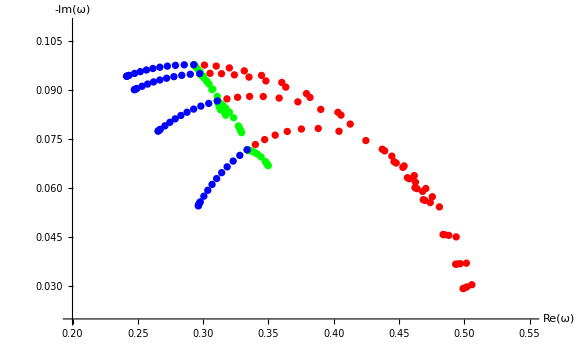

```mathematica
(*Plotting quasinormal mode frequencies for l=1*)
ListPlot[{Table[{Re[ω/.findfreq[a,0,1,1,100,"quasinormal","no"]],-Im[ω/.findfreq[a,0,1,1,100,"quasinormal","no"]]},{a,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,0.92,0.94,0.95,0.96,0.98,0.99,0.995}}],
Table[{Re[ω/.findfreq[a,0.1,1,1,100,"quasinormal","no"]],-Im[ω/.findfreq[a,0.1,1,1,100,"quasinormal","no"]]},{a,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,0.92,0.94,0.95,0.96,0.98,0.99,0.995}}],
Table[{Re[ω/.findfreq[a,0.2,1,1,100,"quasinormal","no"]],-Im[ω/.findfreq[a,0.2,1,1,100,"quasinormal","no"]]},{a,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,0.92,0.94,0.95,0.96,0.98,0.99,0.995}}],
Table[{Re[ω/.findfreq[a,0.3,1,1,100,"quasinormal","no"]],-Im[ω/.findfreq[a,0.3,1,1,100,"quasinormal","no"]]},{a,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,0.92,0.94,0.95,0.96,0.98,0.99,0.995}}],
Table[{Re[ω/.findfreq[a,0,1,0,100,"quasinormal","no"]],-Im[ω/.findfreq[a,0,1,0,100,"quasinormal","no"]]},{a,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,0.92,0.94,0.95,0.96,0.98,0.99,0.995}}],
Table[{Re[ω/.findfreq[a,0.1,1,0,100,"quasinormal","no"]],-Im[ω/.findfreq[a,0.1,1,0,100,"quasinormal","no"]]},{a,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,0.92,0.94,0.95,0.96,0.98,0.99,0.995}}],
Table[{Re[ω/.findfreq[a,0.2,1,0,100,"quasinormal","no"]],-Im[ω/.findfreq[a,0.2,1,0,100,"quasinormal","no"]]},{a,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,0.92,0.94,0.95,0.96,0.98,0.99,0.995}}],
Table[{Re[ω/.findfreq[a,0.3,1,0,100,"quasinormal","no"]],-Im[ω/.findfreq[a,0.3,1,0,100,"quasinormal","no"]]},{a,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,0.92,0.94,0.95,0.96,0.98,0.99,0.995}}],
Table[{Re[ω/.findfreq[a,0,1,-1,100,"quasinormal","no"]],-Im[ω/.findfreq[a,0,1,-1,100,"quasinormal","no"]]},{a,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,0.92,0.94,0.95,0.96,0.98,0.99,0.995}}],
Table[{Re[ω/.findfreq[a,0.1,1,-1,100,"quasinormal","no"]],-Im[ω/.findfreq[a,0.1,1,-1,100,"quasinormal","no"]]},{a,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,0.92,0.94,0.95,0.96,0.98,0.99,0.995}}],
Table[{Re[ω/.findfreq[a,0.2,1,-1,100,"quasinormal","no"]],-Im[ω/.findfreq[a,0.2,1,-1,100,"quasinormal","no"]]},{a,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,0.92,0.94,0.95,0.96,0.98,0.99,0.995}}],
Table[{Re[ω/.findfreq[a,0.3,1,-1,100,"quasinormal","no"]],-Im[ω/.findfreq[a,0.3,1,-1,100,"quasinormal","no"]]},{a,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,0.92,0.94,0.95,0.96,0.98, 0.99,0.995}}]},PlotStyle->{Red,Red,Red,Red,Green,Green,Green,Green,Blue,Blue,Blue,Blue},Joined->False,Mesh->True,AxesLabel->{"Re(ω)","-Im(ω)"},ImageSize->Large,PlotRange->{{0.2,0.55},{0.02,0.11}}]
```

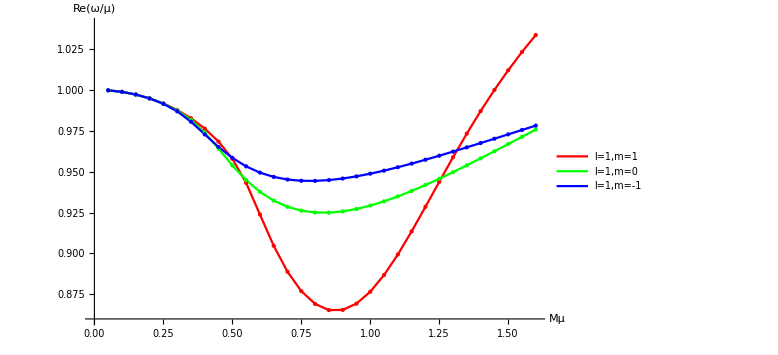

```mathematica
(*Plotting bound state frequency spectra (Re) for a=0.99 and l=1*)
ListPlot[{Table[{μ,Re[ω/.findfreq[0.99,μ,1,1,200,"bound","no"]]/μ},{μ,0.05,1.6,0.05}],
Table[{μ,Re[ω/.findfreq[0.99,μ,1,0,200,"bound","no"]]/μ},{μ,0.05,1.6,0.05}],
Table[{μ,Re[ω/.findfreq[0.99,μ,1,-1,200,"bound","no"]]/μ},{μ,0.05,1.6,0.05}]},ImageSize->Large,PlotRange->{{0,1.6},{0.86,1.04}},Joined->True,Mesh->True,MeshStyle->PointSize[Medium],AxesLabel->{"Mμ","Re(ω/μ)"},PlotStyle->{Red,Green,Blue},PlotLegends->{"l=1,m=1","l=1,m=0","l=1,m=-1"}]
```

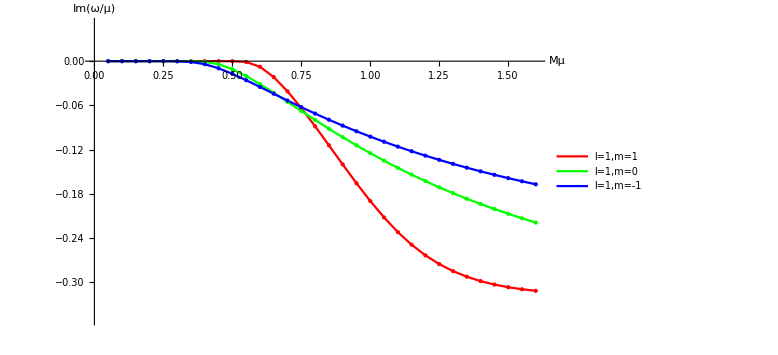

```mathematica
(*Plotting bound state frequency spectra (Im) for a=0.99 and l=1*)
ListPlot[{Table[{μ,Im[ω/.findfreq[0.99,μ,1,1,200,"bound","no"]]/μ},{μ,0.05,1.6,0.05}],
Table[{μ,Im[ω/.findfreq[0.99,μ,1,0,200,"bound","no"]]/μ},{μ,0.05,1.6,0.05}],
Table[{μ,Im[ω/.findfreq[0.99,μ,1,-1,200,"bound","no"]]/μ},{μ,0.05,1.6,0.05}]},ImageSize->Large,PlotRange->{{0,1.6},{-0.35,0.05}},Joined->True,Mesh->True,MeshStyle->PointSize[Medium],AxesLabel->{"Mμ","Im(ω/μ)"},PlotStyle->{Red,Green,Blue},PlotLegends->{"l=1,m=1","l=1,m=0","l=1,m=-1"}]
```

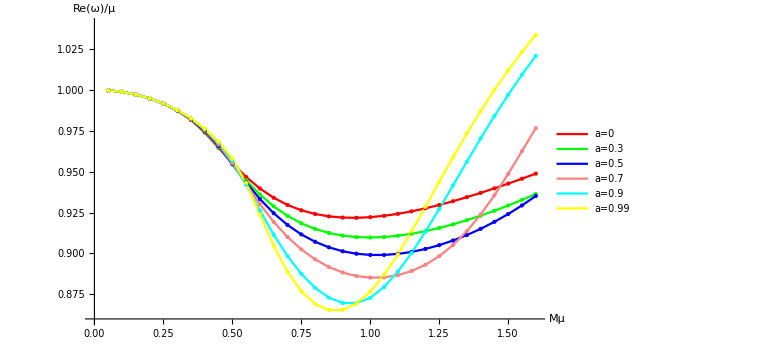

```mathematica
(*Plotting bound state frequency spectra (Re) for l=1,m=1 and different spins*)
ListPlot[{Table[{μ,Re[ω/.findfreq[0,μ,1,1,200,"bound","no"]]/μ},{μ,0.05,1.6,0.05}],
Table[{μ,Re[ω/.findfreq[0.3,μ,1,1,200,"bound","no"]]/μ},{μ,0.05,1.6,0.05}],Table[{μ,Re[ω/.findfreq[0.5,μ,1,1,200,"bound","no"]]/μ},{μ,0.05,1.6,0.05}],Table[{μ,Re[ω/.findfreq[0.7,μ,1,1,200,"bound","no"]]/μ},{μ,0.05,1.6,0.05}],Table[{μ,Re[ω/.findfreq[0.9,μ,1,1,200,"bound","no"]]/μ},{μ,0.05,1.6,0.05}],Table[{μ,Re[ω/.findfreq[0.99,μ,1,1,200,"bound","no"]]/μ},{μ,0.05,1.6,0.05}]},ImageSize->Large,PlotRange->{{0,1.6},{0.86,1.04}},Joined->True,Mesh->True,MeshStyle->PointSize[Medium],AxesLabel->{"Mμ","Re(ω)/μ"},PlotStyle->{Red,Green,Blue,Pink,Cyan,Yellow,Black},PlotLegends->{"a=0","a=0.3","a=0.5","a=0.7","a=0.9","a=0.99"}]
```

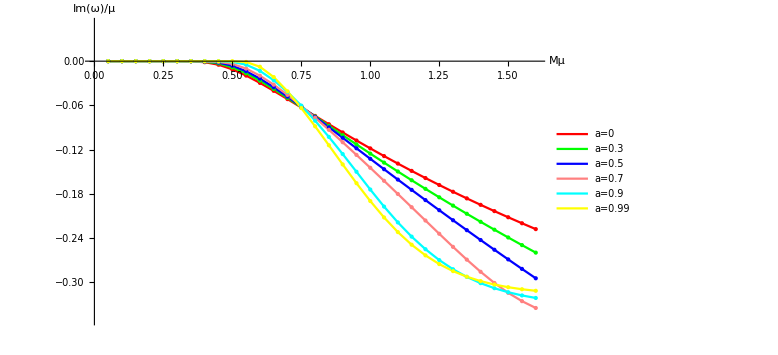

```mathematica
(*Plotting bound state frequency spectra (Im) for l=1,m=1 and different spins*)
ListPlot[{Table[{μ,Im[ω/.findfreq[0,μ,1,1,200,"bound","no"]]/μ},{μ,0.05,1.6,0.05}],
Table[{μ,Im[ω/.findfreq[0.3,μ,1,1,200,"bound","no"]]/μ},{μ,0.05,1.6,0.05}],Table[{μ,Im[ω/.findfreq[0.5,μ,1,1,200,"bound","no"]]/μ},{μ,0.05,1.6,0.05}],Table[{μ,Im[ω/.findfreq[0.7,μ,1,1,200,"bound","no"]]/μ},{μ,0.05,1.6,0.05}],Table[{μ,Im[ω/.findfreq[0.9,μ,1,1,200,"bound","no"]]/μ},{μ,0.05,1.6,0.05}],Table[{μ,Im[ω/.findfreq[0.99,μ,1,1,200,"bound","no"]]/μ},{μ,0.05,1.6,0.05}]},ImageSize->Large,PlotRange->{{0,1.6},{-0.35,0.05}},Joined->True,Mesh->True,MeshStyle->PointSize[Medium],AxesLabel->{"Mμ","Im(ω)/μ"},PlotStyle->{Red,Green,Blue,Pink,Cyan,Yellow,Black},PlotLegends->{"a=0","a=0.3","a=0.5","a=0.7","a=0.9","a=0.99"}]
```

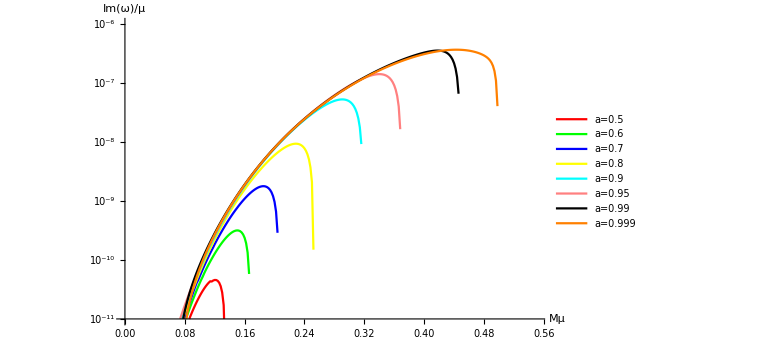

```mathematica
(*Plotting gdecay width as a function of gravtational coupling for l=1,m=1 mode*)
ListLogPlot[{Table[{μ,Im[ω/.findfreq[0.5,μ,1,1,200,"bound","no"]]/μ},{μ,0.06,0.2,0.002}],
Table[{μ,Im[ω/.findfreq[0.6,μ,1,1,200,"bound","no"]]/μ},{μ,0.06,0.2,0.002}],Table[{μ,Im[ω/.findfreq[0.7,μ,1,1,200,"bound","no"]]/μ},{μ,0.06,0.25,0.002}],Table[{μ,Im[ω/.findfreq[0.8,μ,1,1,200,"bound","no"]]/μ},{μ,0.06,0.3,0.002}],Table[{μ,Im[ω/.findfreq[0.9,μ,1,1,200,"bound","no"]]/μ},{μ,0.06,0.35,0.002}],Table[{μ,Im[ω/.findfreq[0.95,μ,1,1,200,"bound","no"]]/μ},{μ,0.06,0.4,0.002}],Table[{μ,Im[ω/.findfreq[0.99,μ,1,1,200,"bound","no"]]/μ},{μ,0.06,0.5,0.002}],Table[{μ,Im[ω/.findfreq[0.999,μ,1,1,600,"bound","no"]]/μ},{μ,0.06,0.55,0.002}]},ImageSize->Large,PlotRange->{{0,0.55},{10^-11,10^-6}},Joined->True,AxesLabel->{"Mμ","Im(ω)/μ"},PlotStyle->{Red,Green,Blue,Yellow,Cyan,Pink,Black,Orange},PlotLegends->{"a=0.5","a=0.6","a=0.7","a=0.8","a=0.9","a=0.95","a=0.99","a=0.999"}]
```